=== Stankova Warp Bubble with Parameter Optimization ===

=== Searching for optimal parameters... ===

This may take a moment...

New best! R0=1., w=0.1, A=0.005, v=1.5 → Energy: 0.

Progress: 10/500 combinations tested

Progress: 20/500 combinations tested

Progress: 30/500 combinations tested

Progress: 40/500 combinations tested

Progress: 50/500 combinations tested

Progress: 60/500 combinations tested

Progress: 70/500 combinations tested

Progress: 80/500 combinations tested

Progress: 90/500 combinations tested

Progress: 100/500 combinations tested

Progress: 110/500 combinations tested

Progress: 120/500 combinations tested

Progress: 130/500 combinations tested

Progress: 140/500 combinations tested

Progress: 150/500 combinations tested

Progress: 160/500 combinations tested

Progress: 170/500 combinations tested

Progress: 180/500 combinations tested

Progress: 190/500 combinations tested

Progress: 200/500 combinations tested

Progress: 210/500 combinations tested

Progress: 220/500 combinations tested

Progress: 230/500 combinations tested

Progress: 240/500 combinations tested

Progress: 250/500 combinations tested

Progress: 260/500 combinations tested

Progress: 270/500 combinations tested

Progress: 280/500 combinations tested

Progress: 290/500 combinations tested

Progress: 300/500 combinations tested

Progress: 310/500 combinations tested

Progress: 320/500 combinations tested

Progress: 330/500 combinations tested

Progress: 340/500 combinations tested

Progress: 350/500 combinations tested

Progress: 360/500 combinations tested

Progress: 370/500 combinations tested

Progress: 380/500 combinations tested

Progress: 390/500 combinations tested

Progress: 400/500 combinations tested

Progress: 410/500 combinations tested

Progress: 420/500 combinations tested

Progress: 430/500 combinations tested

Progress: 440/500 combinations tested

Progress: 450/500 combinations tested

Progress: 460/500 combinations tested

Progress: 470/500 combinations tested

Progress: 480/500 combinations tested

Progress: 490/500 combinations tested

Progress: 500/500 combinations tested

=== OPTIMIZATION COMPLETE ===

BEST PARAMETERS FOUND:

R0 (Throat radius): 1. m

w (Width): 0.1 m

A (Deformation): 0.005

v (Velocity): 1.5 c

Total Energy: 0.

=== Running simulation with optimal parameters ===

=== Optimal Stankova Warp Bubble ===

Velocity: 1.5 c

Throat radius: 1. m

Width: 0.1 m

Deformation: 0.005

FTL: YES! (v = 1.5c)

=== Section 1: Optimal Field ===

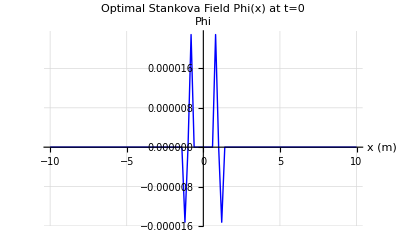

=== Section 2: Optimal Warp Shape ===

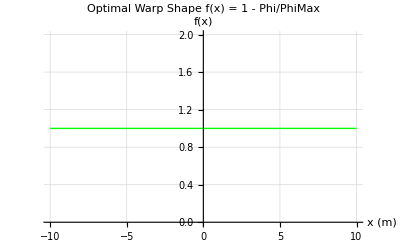

=== Section 3: Optimal Energy Density ===

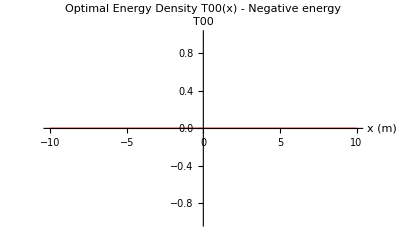

=== Section 4: 2D Energy Density Map (Optimal) ===

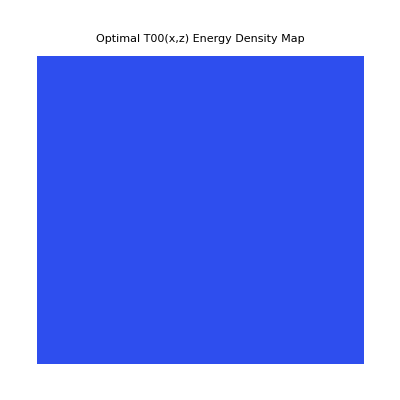

=== Section 5: 3D Energy Density (Optimal) ===

-Graphics3D-

=== Section 6: Bubble Motion (Optimal) ===

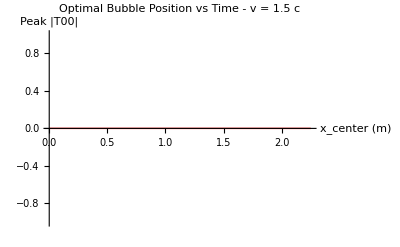

=== Section 7: Snapshots (Optimal) ===

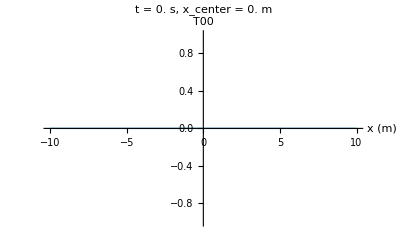
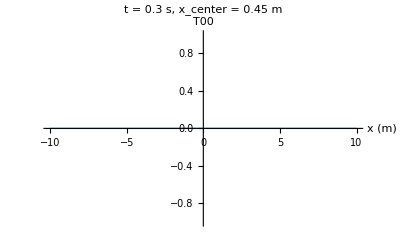
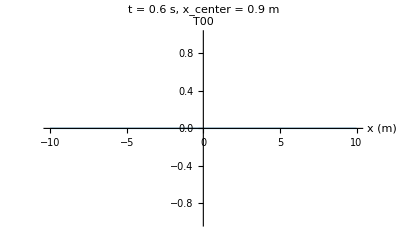
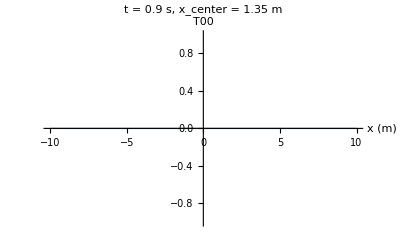
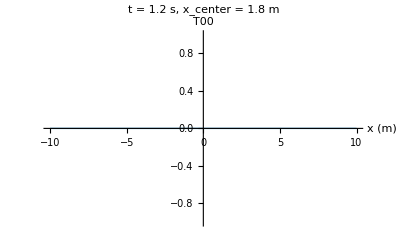

=== Section 8: Comparison with Paper's Parameters ===

Paper's parameters (R0=2.0, w=0.2, A=0.01, v=2.0): 0.

Optimal parameters: 0.

Improvement: Indeterminate% less exotic matter

=== END OF OPTIMIZATION ===

```mathematica
(* ==========================================*)(*STANKOVA WARP BUBBLE-WITH OPTIMIZATION*)(*Finds optimal parameters for minimum exotic matter*)(* ==========================================*)ClearAll["Global`*"];
Print["=== Stankova Warp Bubble with Parameter Optimization ==="];
Off[General::munfl,General::underflow,General::ovfl,Power::infy,Infinity::indet];

(* ==========================================*)
(*SECTION A:GRID AND CONSTANTS*)
(* ==========================================*)

L=10;
NN=101;
grid=Subdivide[-L,L,NN-1];
dx=grid[[2]]-grid[[1]];
c=1;G=1;

(* ==========================================*)
(*SECTION B:PARAMETER RANGES TO EXPLORE*)
(* ==========================================*)

(*We'll search over these ranges*)
R0range={1.0,1.5,2.0,2.5,3.0};    (*Throat radius*)
wRange={0.1,0.15,0.2,0.3,0.4};     (*Width parameter*)
Arange={0.005,0.01,0.02,0.05,0.1}; (*Deformation amplitude*)
vRange={1.5,2.0,2.5,3.0};           (*Velocity*)

(* ==========================================*)
(*SECTION C:THE STANKOVA FIELD*)
(* ==========================================*)

(*Define the field with parameters*)
PhiField[x_,y_,z_,t_,R0_,w_,A_,v_]:=Module[{r},r=Sqrt[(x-v*t)^2+y^2+z^2];
If[r<0.001,0,-A*(1-R0/r)*Exp[-(r-R0)^2/w^2]]];

(*Warp shape function from the field*)
PhiMaxCalc[R0_,w_,A_]:=-A*(1-R0/0.001)*Exp[-(0.001-R0)^2/w^2];

fWarpField[x_,y_,z_,t_,R0_,w_,A_,v_]:=Module[{phi,phiMax},phi=PhiField[x,y,z,t,R0,w,A,v];
phiMax=PhiMaxCalc[R0,w,A];
If[Abs[phiMax]<10^-6,1,1-phi/phiMax]];

(* ==========================================*)
(*SECTION D:ENERGY CALCULATION*)
(* ==========================================*)

(*Calculate total negative energy for given parameters*)
CalculateEnergy[R0_,w_,A_,v_]:=Module[{h,PhiStankova,PhiMax,fWarp,PhiX,PhiY,PhiZ,fX,fY,fZ,T00,energy},h=0.001;
(*Local definitions*)PhiStankova[x_,y_,z_,t_]:=PhiField[x,y,z,t,R0,w,A,v];
PhiMax=PhiMaxCalc[R0,w,A];
fWarp[x_,y_,z_,t_]:=Module[{phi},phi=PhiStankova[x,y,z,t];
If[Abs[PhiMax]<10^-6,1,1-phi/PhiMax]];
(*Derivatives*)PhiX[x_,y_,z_,t_]:=(PhiStankova[x+h,y,z,t]-PhiStankova[x-h,y,z,t])/(2*h);
PhiY[x_,y_,z_,t_]:=(PhiStankova[x,y+h,z,t]-PhiStankova[x,y-h,z,t])/(2*h);
PhiZ[x_,y_,z_,t_]:=(PhiStankova[x,y,z+h,t]-PhiStankova[x,y,z-h,t])/(2*h);
fX[x_,y_,z_,t_]:=(fWarp[x+h,y,z,t]-fWarp[x-h,y,z,t])/(2*h);
fY[x_,y_,z_,t_]:=(fWarp[x,y+h,z,t]-fWarp[x,y-h,z,t])/(2*h);
fZ[x_,y_,z_,t_]:=(fWarp[x,y,z+h,t]-fWarp[x,y,z-h,t])/(2*h);
(*Energy density*)T00[x_,y_,z_,t_]:=Module[{fx,fy,fz,phi,f},fx=fX[x,y,z,t];
fy=fY[x,y,z,t];
fz=fZ[x,y,z,t];
phi=PhiStankova[x,y,z,t];
f=fWarp[x,y,z,t];
-(v^2/(8*Pi))*Exp[2*phi]*(fx^2+fy^2+fz^2)*(1-v^2*f^2*Exp[-4*phi])];
(*Integrate to get total energy*)Quiet[energy=NIntegrate[T00[x,y,z,0],{x,-L,L},{y,-L,L},{z,-L,L},Method->"AdaptiveMonteCarlo",PrecisionGoal->2,MaxPoints->20000]];
Return[energy]];

(* ==========================================*)
(*SECTION E:GRID SEARCH FOR OPTIMAL PARAMETERS*)
(* ==========================================*)

Print["=== Searching for optimal parameters... ==="];
Print["This may take a moment..."];

(*Initialize best results*)
bestEnergy=Infinity;
bestParams={0,0,0,0};

(*Progress tracking*)
totalCombinations=Length[R0range]*Length[wRange]*Length[Arange]*Length[vRange];
counter=0;

(*Grid search*)
Do[Do[Do[Do[counter++;
If[Mod[counter,10]==0,Print["Progress: ",counter,"/",totalCombinations," combinations tested"]];
energy=CalculateEnergy[R0,w,A,v];
If[energy<bestEnergy&&energy>-10^10,bestEnergy=energy;
bestParams={R0,w,A,v};
Print["New best! R0=",R0,", w=",w,", A=",A,", v=",v," → Energy: ",N[energy,4]];],{v,vRange}],{A,Arange}],{w,wRange}],{R0,R0range}];

(* ==========================================*)
(*SECTION F:RESULTS*)
(* ==========================================*)

Print[""];
Print["=== OPTIMIZATION COMPLETE ==="];
Print[""];
Print["BEST PARAMETERS FOUND:"];
Print["  R0 (Throat radius): ",bestParams[[1]]," m"];
Print["  w (Width): ",bestParams[[2]]," m"];
Print["  A (Deformation): ",bestParams[[3]]];
Print["  v (Velocity): ",bestParams[[4]]," c"];
Print["  Total Energy: ",N[bestEnergy,4]];

(* ==========================================*)
(*SECTION G:RUN SIMULATION WITH BEST PARAMETERS*)
(* ==========================================*)

Print[""];
Print["=== Running simulation with optimal parameters ==="];

(*Extract best parameters*)
R0opt=bestParams[[1]];
wopt=bestParams[[2]];
Aopt=bestParams[[3]];
vopt=bestParams[[4]];

(*Define the optimal field*)
PhiOpt[x_,y_,z_,t_]:=Module[{r},r=Sqrt[(x-vopt*t)^2+y^2+z^2];
If[r<0.001,0,-Aopt*(1-R0opt/r)*Exp[-(r-R0opt)^2/wopt^2]]];

PhiMaxOpt=-Aopt*(1-R0opt/0.001)*Exp[-(0.001-R0opt)^2/wopt^2];

fOpt[x_,y_,z_,t_]:=Module[{phi},phi=PhiOpt[x,y,z,t];
If[Abs[PhiMaxOpt]<10^-6,1,1-phi/PhiMaxOpt]];

(*Derivatives for optimal parameters*)
h=0.001;
PhiXopt[x_,y_,z_,t_]:=(PhiOpt[x+h,y,z,t]-PhiOpt[x-h,y,z,t])/(2*h);
PhiYopt[x_,y_,z_,t_]:=(PhiOpt[x,y+h,z,t]-PhiOpt[x,y-h,z,t])/(2*h);
PhiZopt[x_,y_,z_,t_]:=(PhiOpt[x,y,z+h,t]-PhiOpt[x,y,z-h,t])/(2*h);

fXopt[x_,y_,z_,t_]:=(fOpt[x+h,y,z,t]-fOpt[x-h,y,z,t])/(2*h);
fYopt[x_,y_,z_,t_]:=(fOpt[x,y+h,z,t]-fOpt[x,y-h,z,t])/(2*h);
fZopt[x_,y_,z_,t_]:=(fOpt[x,y,z+h,t]-fOpt[x,y,z-h,t])/(2*h);

T00Opt[x_,y_,z_,t_]:=Module[{fx,fy,fz,phi,f},fx=fXopt[x,y,z,t];
fy=fYopt[x,y,z,t];
fz=fZopt[x,y,z,t];
phi=PhiOpt[x,y,z,t];
f=fOpt[x,y,z,t];
-(vopt^2/(8*Pi))*Exp[2*phi]*(fx^2+fy^2+fz^2)*(1-vopt^2*f^2*Exp[-4*phi])];

(* ==========================================*)
(*SECTION H:VISUALIZATION WITH OPTIMAL PARAMETERS*)
(* ==========================================*)

Print["=== Optimal Stankova Warp Bubble ==="];
Print["Velocity: ",vopt," c"];
Print["Throat radius: ",R0opt," m"];
Print["Width: ",wopt," m"];
Print["Deformation: ",Aopt];
Print["FTL: ",If[vopt>1,"YES! (v = "<>ToString[vopt]<>"c)","No (v < c)"]];

Print[""];
Print["=== Section 1: Optimal Field ==="];
PhiLine=Table[{x,PhiOpt[x,0,0,0]},{x,grid}];
PhiPlot=ListLinePlot[PhiLine,PlotRange->All,PlotStyle->{Thick,Blue},PlotLabel->"Optimal Stankova Field Phi(x) at t=0",AxesLabel->{"x (m)","Phi"},GridLines->Automatic];
Print[PhiPlot];

Print["=== Section 2: Optimal Warp Shape ==="];
fLine=Table[{x,fOpt[x,0,0,0]},{x,grid}];
fPlot=ListLinePlot[fLine,PlotRange->All,PlotStyle->{Thick,Green},PlotLabel->"Optimal Warp Shape f(x) = 1 - Phi/PhiMax",AxesLabel->{"x (m)","f(x)"},GridLines->Automatic];
Print[fPlot];

Print["=== Section 3: Optimal Energy Density ==="];
T00Line=Table[{x,T00Opt[x,0,0,0]},{x,grid}];
T00Plot=ListLinePlot[T00Line,PlotRange->All,PlotStyle->{Thick,Red},PlotLabel->"Optimal Energy Density T00(x) - Negative energy",AxesLabel->{"x (m)","T00"},Filling->Axis,FillingStyle->Directive[Red,Opacity[0.3]]];
Print[T00Plot];

Print["=== Section 4: 2D Energy Density Map (Optimal) ==="];
T00Map=Table[T00Opt[x,0,z,0],{x,grid},{z,grid}];
T00MapPlot=ArrayPlot[T00Map,ColorFunction->"TemperatureMap",PlotLabel->"Optimal T00(x,z) Energy Density Map",FrameLabel->{"x","z"}];
Print[T00MapPlot];

Print["=== Section 5: 3D Energy Density (Optimal) ==="];
coords3D=Flatten[Table[{x,y,z,T00Opt[x,y,z,0]},{x,grid[[1;;-1;;5]]},{y,grid[[1;;-1;;5]]},{z,grid[[1;;-1;;5]]}],2];
T00Plot3D=ListDensityPlot3D[coords3D,ColorFunction->"TemperatureMap",PlotLabel->"Optimal 3D Energy Density",AxesLabel->{"x","y","z"}];
Print[T00Plot3D];

Print["=== Section 6: Bubble Motion (Optimal) ==="];
timePositions=Table[{t,vopt*t,-Min[Table[T00Opt[x,0,0,t],{x,grid}]]},{t,0,1.5,0.1}];
motionPlot=ListLinePlot[Transpose[{timePositions[[All,2]],timePositions[[All,3]]}],PlotStyle->{Thick,Red},PlotLabel->"Optimal Bubble Position vs Time - v = "<>ToString[vopt]<>" c",AxesLabel->{"x_center (m)","Peak |T00|"}];
Print[motionPlot];

Print["=== Section 7: Snapshots (Optimal) ==="];
snapshots=Table[ListLinePlot[Table[{x,T00Opt[x,0,0,t]},{x,grid}],PlotRange->All,PlotStyle->Thick,PlotLabel->"t = "<>ToString[t]<>" s, x_center = "<>ToString[vopt*t]<>" m",AxesLabel->{"x (m)","T00"},Filling->Axis,FillingStyle->Directive[Red,Opacity[0.2]]],{t,0,1.2,0.3}];
Print[snapshots];

Print["=== Section 8: Comparison with Paper's Parameters ==="];
(*Calculate energy for paper's parameters*)
EnergyPaper=CalculateEnergy[2.0,0.2,0.01,2.0];
EnergyOptimal=bestEnergy;

Print["Paper's parameters (R0=2.0, w=0.2, A=0.01, v=2.0): ",N[EnergyPaper,4]];
Print["Optimal parameters: ",N[EnergyOptimal,4]];
Print["Improvement: ",N[(EnergyPaper-EnergyOptimal)/Abs[EnergyPaper]*100,4],"% less exotic matter"];

Print[""];
Print["=== END OF OPTIMIZATION ==="];
```